```mathematica
Subscript[k, 7][x_,r_,a_,t_]=Sqrt[(u+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)]
```

```mathematica
Subscript[n, 7(2)][r_]=2 r^2 Integrate[AiryAi[x](Sqrt[(u+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)]/(2a Pi))^3 BesselJ[3,2a Sqrt[(u+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)]],{a,t,x}∈ImplicitRegion[(u+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)≥0&&a≥0&&-1≤t≤1,{a,t,x}]]
```

2 r^2 ∫_({a,t,x}∈ImplicitRegion[2/(3 r)+u+4/(3 √(r^2+a^2-2 r a t))-(((2/(√(r^2+a^2-2 r a t))r)^2)^(1/3) x)/3^(1/3)≥0&&a≥0&&-1≤t≤1,{a,t,x}]) (AiryAi[x] BesselJ[3,2 a √(2/(3 r)+4/(3 √(a^2+r^2-2 a r t))+u-(x ((2/(√(a^2+r^2-2 a r t))r)^2)^(1/3))/3^(1/3))] (2/(3 r)+4/(3 √(a^2+r^2-2 a r t))+u-(x ((2/(√(a^2+r^2-2 a r t))r)^2)^(1/3))/3^(1/3))^(3/2))/(8 a^3 π^3)

```mathematica
Plot[2 r^2 Integrate[AiryAi[x](Sqrt[(-0.48075+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)]/(2a Pi))^3 BesselJ[3,2a Sqrt[(-0.48075+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)]],{a,t}∈ImplicitRegion[(-0.48075+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)≥0&&a≥0&&-1≤t≤1,{a,t}],{x,-Infinity,Infinity}],{r,0,10}]
```

GreaterEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of GreaterEqual::nord
     will be suppressed during this calculation.

DiscretizeRegion::defbnds: Unable to compute bounds for the region. Using default bounds of {-1, 1} in all dimensions.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region RegionProduct[«2»].

DiscretizeRegion::defbnds: Unable to compute bounds for the region. Using default bounds of {-1, 1} in all dimensions.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region RegionProduct[«2»].

DiscretizeRegion::defbnds: Unable to compute bounds for the region. Using default bounds of {-1, 1} in all dimensions.

General::stop: Further output of DiscretizeRegion::defbnds will be suppressed during this calculation.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region RegionProduct[«2»].

General::stop: Further output of DiscretizeRegion::drf will be suppressed during this calculation.

```mathematica
(Sqrt[(-0.48075+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)]/(2a Pi))^3 BesselJ[3,2a Sqrt[(-0.48075+(1/3)(2/r)+(2/3)(2/Sqrt[a^2+r^2-2a r t]))-x((1/3)Grad[2/Sqrt[a^2+r^2-2a r t],r]^2)^(1/3)]]
```

```mathematica
Solve[(x-r)^2/x==z,x]
```

{{x→1/2 (2 r+z-√z √(4 r+z))},{x→1/2 (2 r+z+√z √(4 r+z))}}

```mathematica
Solve[(x+r)^2/x==z,x]
```

{{x→1/2 (-2 r+z-√(-4 r z+z^2))},{x→1/2 (-2 r+z+√(-4 r z+z^2))}}

```mathematica
D[1/2 (2 r+z-√z √(4 r+z)),z]
```

1/2 (1-(√z)/(2 √(4 r+z))-(√(4 r+z))/(2 √z))

```mathematica
Simplify[1/2 (1-(√z)/(2 √(4 r+z))-(√(4 r+z))/(2 √z))]
```

(-2 r-z+√z √(4 r+z))/(2 √z √(4 r+z))

```mathematica
Subscript[n, TF(10)][r_]=((Sqrt[-0.164414+2/r])^3)*HeavisideTheta[-0.164414+2/r]/(3Pi^2)
```

```mathematica
Solve[2(-2/u)+u (-2/u)^2/2==2]
```

{{u→-1}}

```mathematica
Solve[2(-2/u)+u (-2/u)^2/2==10]
```

{{u→-1/5}}

```mathematica
Solve[2(-2/u)+u (-2/u)^2/2==28]
```

{{u→-1/14}}

```mathematica
(u+2/r)HeavisideTheta[u+2/r]/(2Pi)
```

((2/r+u) HeavisideTheta[2/r+u])/(2 π)

```mathematica
r(2/r+u)
```

r (2/r+u)

```mathematica
Simplify[r (2/r+u)]
```

```mathematica
Integrate[2+r u,{r,0,-2/u}]
```

-2/u

```mathematica
Solve[-2/u==2]
```

{{u→-1}}

```mathematica
Subscript[n, 2(2)][r_]=∫_({a,θ}∈ImplicitRegion[(2/1)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[2,2 a √(-1+2/(√(a^2+r^2-2 a r Cos[θ])))] (-1+2/(√(a^2+r^2-2 a r Cos[θ]))))/(a π)
```

Get::noopen: Cannot open CloudObject`.

∫_({a,θ}∈ImplicitRegion[4>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[2,2 a √(-1+2/(√(a^2+r^2-2 a r Cos[θ])))] (-1+2/(√(a^2+r^2-2 a r Cos[θ]))))/(a π)

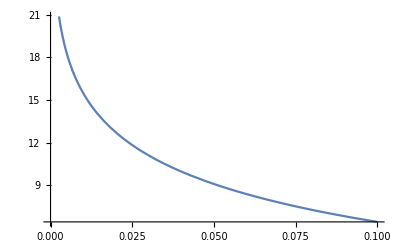

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[4>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[2,2 a √(-1+2/(√(a^2+r^2-2 a r Cos[θ])))] (-1+2/(√(a^2+r^2-2 a r Cos[θ]))))/(a π),{r,0,0.1}]
```

```mathematica
∫_({a,θ}∈ImplicitRegion[4>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[1,2 a √(2/Abs[r+a])] √(2/Abs[r+a]))/(a π)
```

```mathematica
Integrate[Sqrt[u+2/r]/Pi,r]
```

```mathematica
((-2/u) √(2/(-2/u)+u)+Log[1+(-2/u) (u+√u √(2/(-2/u)+u))]/(√u))/π
```

ⅈ/(√u)

```mathematica
1+(-2/u) (u+√u √(2/(-2/u)+u))
```

-1

```mathematica
Integrate[(BesselJ[1,2 a √(2/Abs[r+a])] √(2/Abs[r+a]))/(a π),{a,0,Infinity}]
```

∫_0^∞ (√2 BesselJ[1,(2 √2 a)/(√Abs[a+r])])/(a π √Abs[a+r])ⅆa

```mathematica
Plot[{Integrate[(BesselJ[1,2 a √(2/Abs[r+a])] √(2/Abs[r+a]))/(a π),{a,0,Infinity}],Log[E,1/r]/Pi},{r,0,0.01}]
```

$Aborted

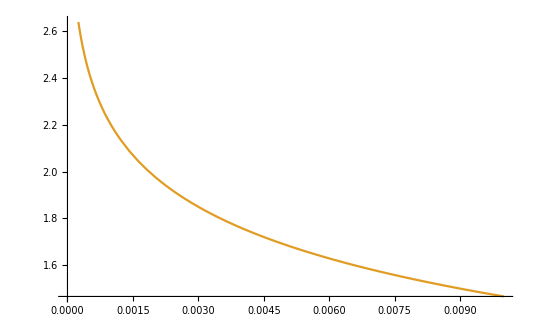

```mathematica
Plot[{Integrate[(BesselJ[1,2 a √(2/Abs[r+a]-1)] √(2/Abs[r+a]-1))/(a π),a∈ImplicitRegion[2/Abs[r+a]-1>0,a]],Log[E,1/r]/Pi},{r,0,0.01}]
```

```mathematica
Plot[{Integrate[(BesselJ[1,2 a √(2/Abs[r+a]-1)] √(2/Abs[r+a]-1))/(a π),a∈ImplicitRegion[2/Abs[r+a]-1>0,a]]/(Log[E,1/r]/Pi)},{r,0,0.01}]
```

-Graphics-

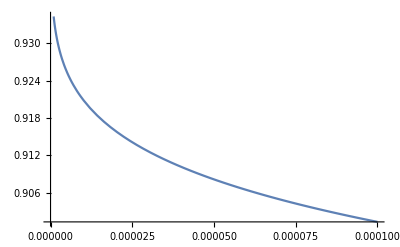

```mathematica
Plot[Integrate[(BesselJ[1,2 a √(2/Abs[r+a]-1)] √(2/Abs[r+a]-1))/(a π),a∈ImplicitRegion[2/Abs[r+a]-1>0&&a>0,a]]/(2Log[E,1/r]/Pi),{r,0,0.0001}]
```

```mathematica
Limit[Integrate[(BesselJ[1,2 a √(2/Abs[r+a]-1)] √(2/Abs[r+a]-1))/(a π),a∈ImplicitRegion[2/Abs[r+a]-1>0&&a>0,a]]/(2Log[E,1/r]/Pi),r->0]
```

$Aborted

```mathematica
Limit[Integrate[(BesselJ[1,2 a √(2/Abs[r+a])] √(2/Abs[r+a]))/(a π),a∈ImplicitRegion[a>0,a]]/(2Log[E,1/r]/Pi),r->0]
```

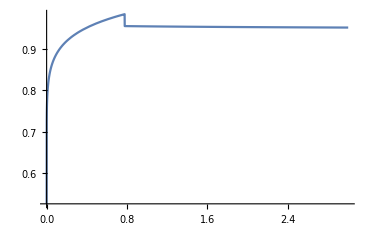

```mathematica
Plot[Integrate[(BesselJ[1,2 a √(2/Abs[r+a])] √(2/Abs[r+a]))/(a π),a∈ImplicitRegion[a>0,a]]/(2Log[E,1/r]/Pi),{r,0,0.00000003},PlotRange->All]
```

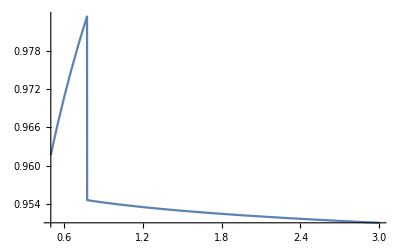

```mathematica
Plot[Integrate[(BesselJ[1,2 a √(2/Abs[r+a])] √(2/Abs[r+a]))/(a π),a∈ImplicitRegion[a>0,a]]/(2Log[E,1/r]/Pi),{r,0.000000005,0.00000003},PlotRange->All]
```

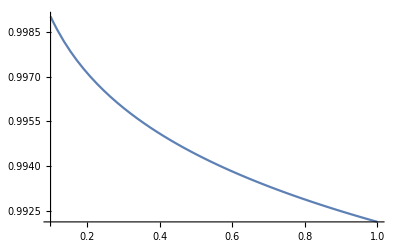

```mathematica
Plot[Integrate[(BesselJ[1,2 a √(2/Abs[r+a])] √(2/Abs[r+a]))/(a 3),a∈ImplicitRegion[a>0,a]]/(2Log[E,1/r]/Pi),{r,0.00000001,0.0000001},PlotRange->All]
```

```mathematica
Solve[y==2Sqrt[2a],a]
```

{{a→y^2/8}}

```mathematica
Integrate[BesselJ[1,y]y/(2Pi (y^2/8)^2),y]
```

-(16 HypergeometricPFQ[{-1/2},{1/2,2},-y^2/4])/(π y)

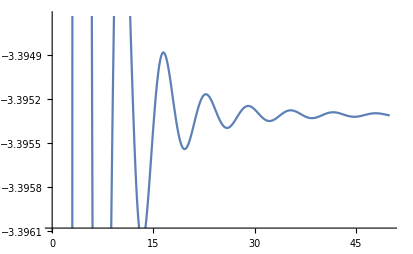

```mathematica
Plot[-(16 HypergeometricPFQ[{-1/2},{1/2,2},-y^2/4])/(π y),{y,0,50}]
```

```mathematica
Limit[(8 HypergeometricPFQ[{-1/2},{1/2,2},-y^2/4])/(y Log[8/y^2]),y->0]
```

Indeterminate

```mathematica
(16 HypergeometricPFQ[{-1/2},{1/2,2},-y^2/4])/(π y)/(2Log[E,1/(y^2/8)]/Pi)
```

(8 HypergeometricPFQ[{-1/2},{1/2,2},-y^2/4])/(y Log[8/y^2])

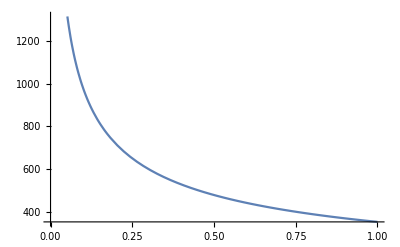

```mathematica
Plot[(16 HypergeometricPFQ[{-1/2},{1/2,2},-(2Sqrt[2a])^2/4])/(π (2Sqrt[2a])Log[E,1/a]),{a,0,0.0000001}]
```

```mathematica
Integrate[(BesselJ[1,2 a √(2/a)] √(2/a))/(Pi a),a∈ImplicitRegion[a>0,a]]
```

∫_(a∈ImplicitRegion[a>0,{a}]) (√2 (1/a)^(3/2) BesselJ[1,(2 √2)/(√(1/a))])/π

```mathematica
FullSimplify[∫_(a∈ImplicitRegion[a>0,{a}]) (√2 (1/a)^(3/2) BesselJ[1,(2 √2)/(√(1/a))])/π]
```

∫_(a∈ImplicitRegion[a>0,{a}]) (2 Hypergeometric0F1Regularized[2,-2 a])/(a π)

```mathematica
Solve[y==2a Sqrt[u+2/a],a]
```

{{a→(-2-√(4+u y^2))/(2 u)},{a→(-2+√(4+u y^2))/(2 u)}}

```mathematica
Integrate[a^-4 DiracDelta[a-u],a]
```

HeavisideTheta[a-u]/u^4

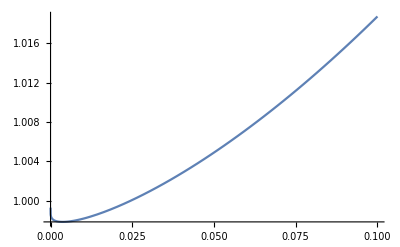

```mathematica
Plot[(64/(Pi))MeijerG[{{},{1}},{{0,0},{-3}},(2 √(-0.164414+2/a) a)^2/4]/((32/(3Pi)Log[E,1/a])),{a,0,0.1}]
```

```mathematica
Plot[(64/(Pi))MeijerG[{{},{1}},{{0,0},{-3}},y^2/4]/((32/(3Pi)Log[E,1/a])),{y,0,0.1}]
```

```mathematica
Integrate[1024/y^4 BesselJ[3,y],y]
```

-64 MeijerG[{{},{1}},{{0,0},{-3}},y^2/4]

```mathematica
(2√(4+u y^2)/y)^-1(1/((-2-√(4+u y^2))/(2 u)))^2+(-2√(4+u y^2)/y)^-1(1/((-2+√(4+u y^2))/(2 u)))^2
```

(2 u^2 y)/(√(4+u y^2) (-2-√(4+u y^2))^2)-(2 u^2 y)/(√(4+u y^2) (-2+√(4+u y^2))^2)

```mathematica
Simplify[(2 u^2 y)/(√(4+u y^2) (-2-√(4+u y^2))^2)-(2 u^2 y)/(√(4+u y^2) (-2+√(4+u y^2))^2)]
```

```mathematica
Integrate[-8/y^3 y BesselJ[1,y],y]
```

2 G_(1,3)^(2,0)(y^2/4|1
0,0,-1)

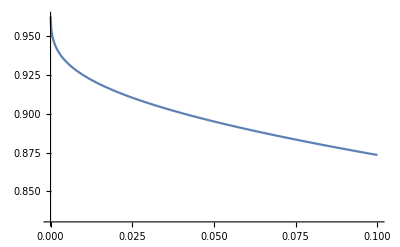

```mathematica
Plot[(2/Pi) MeijerG[{{},{1}},{{0,0},{-1}},y^2/4]/((2/Pi)Log[E,1/((-2+√(4+(-0.164414) y^2))/(2 (-0.164414)))]),{y,0,0.1}]
```

```mathematica
Limit[(2/Pi) MeijerG[{{},{1}},{{0,0},{-1}},y^2/4]/((2/Pi)Log[E,1/((-2+√(4+(-0.164414) y^2))/(2 (-0.164414)))]),y->0]
```

1.

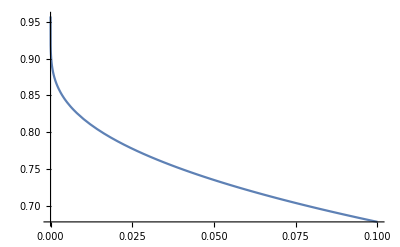

```mathematica
Plot[(2/Pi) MeijerG[{{},{1}},{{0,0},{-1}},(2 √(-0.164414+2/a) a)^2/4]/(((2/Pi))Log[E,1/a]),{a,0,0.1}]
```

```mathematica
Limit[(2/Pi) MeijerG[{{},{1}},{{0,0},{-1}},(2 √(-0.164414+2/a) a)^2/4]/(((2/Pi))Log[E,1/a]),a->0]
```

1.

```mathematica
Solve[y==2r Sqrt[u+2/x],x]
```

{{x→-(8 r^2)/(4 r^2 u-y^2)}}

```mathematica
D[-(8 r^2)/(4 r^2 u-y^2),y]
```

-(16 r^2 y)/((4 r^2 u-y^2)^2)

```mathematica
-(16 r^2 y)/((4 r^2 u-y^2)^2)(-(8 r^2)/(4 r^2 u-y^2))^2 y^3
```

-(1024 r^6 y^4)/((4 r^2 u-y^2)^4)

```mathematica
MeijerGReduce[-(1024 r^6)/((4 r^2 u-y^2)^4),y]
```

```mathematica
MeijerGReduce[BesselJ[3,y],y]
```

```mathematica
MeijerG[{{},{}},{{3/2},{-3/2}},y^2/4]
```

```mathematica
Integrate[-(2 MeijerG[{{-3},{}},{{0},{}},-y^2/(4 r^2 u)])/(3 r^2 u^4)MeijerG[{{},{}},{{7/2},{1/2}},y^2/4],{y,0,Infinity}]
```

ConditionalExpression[-4/3 r^6 BesselK[0,2/(√(-1/(r^2 u)))],Re[r^2 u]≤0||r^2 u∉ℝ]

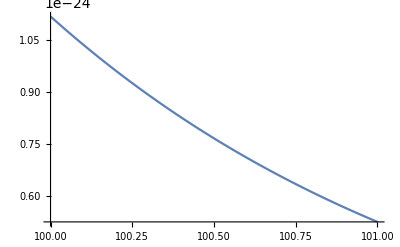

```mathematica
Plot[4/3 r^6 BesselK[0,2/(√(-1/(r^2 (-0.164414))))],{r,100,101}]
```

```mathematica
(2√(4+u y^2)/y)^-1(1/((-2-√(4+u y^2))/(2 u)))^3+(-2√(4+u y^2)/y)^-1(1/((-2+√(4+u y^2))/(2 u)))^3
```

(4 u^3 y)/(√(4+u y^2) (-2-√(4+u y^2))^3)-(4 u^3 y)/(√(4+u y^2) (-2+√(4+u y^2))^3)

```mathematica
Simplify[(4 u^3 y)/(√(4+u y^2) (-2-√(4+u y^2))^3)-(4 u^3 y)/(√(4+u y^2) (-2+√(4+u y^2))^3)]
```

-(8 (16+u y^2))/y^5

```mathematica
Expand[-(8 (16+u y^2))/y^5]
```

-128/y^5-(8 u)/y^3

```mathematica
Integrate[(1/(4Pi))(-128/y^3-(8 u)/y)BesselJ[2,y],y]
```

-(2 ((u (y-2 BesselJ[1,y]))/(2 y)-(8 MeijerG[{{},{2}},{{1,1},{-1}},y^2/4])/y^2))/π

```mathematica
(8 Subscript[G, 1,3]^(2,0)(y^2/4|{{2}, {1,1,-1}}))/y^2
```

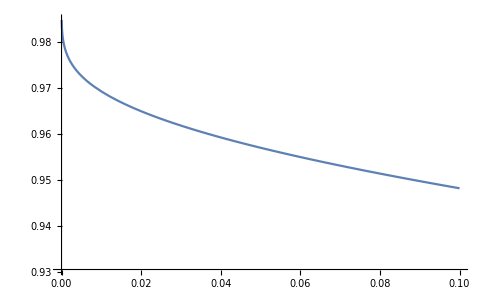

```mathematica
Plot[-(2 ((-0.164414 (y-2 BesselJ[1,y]))/(2 y)-(8 MeijerG[{{},{2}},{{1,1},{-1}},y^2/4])/y^2))/π/((2/Pi)Log[E,1/((-2+√(4+(-0.164414) y^2))/(2 (-0.164414)))]),{y,0,0.1}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

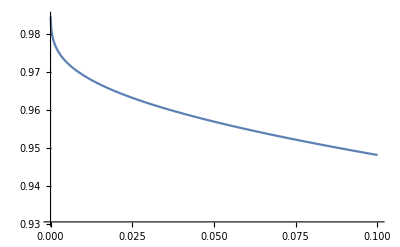

```mathematica
Plot[((16 MeijerG[{{},{2}},{{1,1},{-1}},y^2/4])/y^2)/π/((2/Pi)Log[E,1/((-2+√(4+(-0.164414) y^2))/(2 (-0.164414)))]),{y,0,0.1}]
```

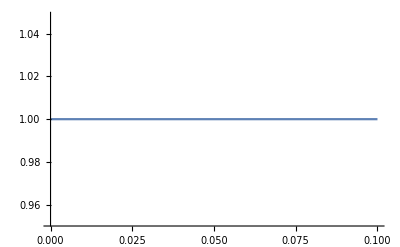

```mathematica
Plot[((16 MeijerG[{{},{2}},{{1,1},{-1}},y^2/4])/y^2)/π/((4 MeijerG[{{},{1}},{{0,0},{-2}},y^2/4])/π),{y,0,0.1}]
```

```mathematica
Plot[(4 MeijerG[{{},{1}},{{0,0},{-2}},y^2/4])/π/((2/Pi)Log[E,1/((-2+√(4+(-0.164414) y^2))/(2 (-0.164414)))]),{y,0,0.1}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
Limit[-(2 ((-0.164414 (y-2 BesselJ[1,y]))/(2 y)-(8 MeijerG[{{},{2}},{{1,1},{-1}},y^2/4])/y^2))/π/((2/Pi)Log[E,1/((-2+√(4+(-0.164414) y^2))/(2 (-0.164414)))]),y->0]
```

1.

```mathematica
Limit[MeijerG[{{},{1}},{{0,0},{-d}},y^2/4]/(Log[E,1/((-2+√(4+(-0.164414) y^2))/(2 (-0.164414)))]),y->0]
```

1./Gamma[1.+d]

```mathematica
(2 √(-0.164414+2/a) a)^2/4
```

```mathematica
Limit[MeijerG[{{},{1}},{{0,0},{-d}},(2 √(u+2/r) r)^2/4]/(Log[E,1/r]),r->0]
```

(1+d)/Gamma[2+d]

```mathematica
FullSimplify[(1+d)/Gamma[2+d]]
```

1/Gamma[1+d]

```mathematica
Limit[MeijerG[{{},{1}},{{0,0},{-d}},(2 √(-0.164414+2/r) r)^2/4]/(Log[E,1/r]),r->0]
```

1./Gamma[1.+d]

```mathematica
Gamma[-s]^2 Gamma[-d-s]Gamma[s]/(Gamma[1+s]^2 Gamma[1+d+s]Gamma[1-s])
```

(Gamma[-d-s] Gamma[-s]^2 Gamma[s])/(Gamma[1-s] Gamma[1+s]^2 Gamma[1+d+s])

```mathematica
FullSimplify[(Gamma[-d-s] Gamma[-s]^2 Gamma[s])/(Gamma[1-s] Gamma[1+s]^2 Gamma[1+d+s])]
```

```mathematica
Integrate[(Gamma[1-s] Gamma[-d-s])/(s^4 Gamma[s] Gamma[1+d+s])(( -0.164414 r^2+2r )^2)^s,s]
```

∫(((2 r-0.164414 r^2)^2)^s Gamma[1-s] Gamma[-d-s])/(s^4 Gamma[s] Gamma[1+d+s])ⅆs

```mathematica
Gamma[-s]Gamma[s]^2/(Gamma[1+d+s])
```

(Gamma[-s] Gamma[s]^2)/Gamma[1+d+s]

```mathematica
FunctionExpand[(Gamma[-s] Gamma[s]^2)/Gamma[1+d+s]]
```

-(π Csc[π s] Gamma[s])/(s Gamma[1+d+s])

```mathematica
Integrate[-(π Csc[π s] Gamma[s])/(s Gamma[1+d+s])z^s,s]
```

-π ∫(z^s Csc[π s] Gamma[s])/(s Gamma[1+d+s])ⅆs

```mathematica
Integrate[(Gamma[-s] Gamma[s]^2)/Gamma[1+d+s] z^s,s]
```

∫(z^s Gamma[-s] Gamma[s]^2)/Gamma[1+d+s]ⅆs

```mathematica
MeijerGReduce[Log[E,1/a],a]
```

```mathematica
Subscript[G, 2,2]^(1,2)(1/a|{{1,1}, {1,0}})-Subscript[G, 2,2]^(1,2)(1/a,-1|{{1,1}, {1,0}})
```

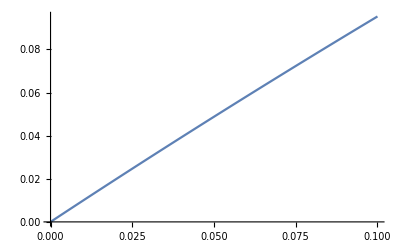

```mathematica
Plot[Subscript[G, 2,2]^(1,2)(1/a,-1|{{1,1}, {1,0}}),{a,0,0.1}]
```

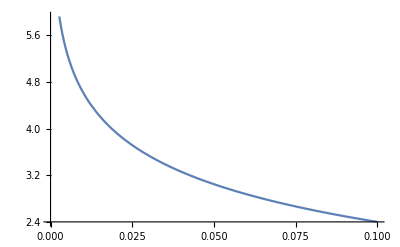

```mathematica
Plot[Subscript[G, 2,2]^(1,2)(1/a|{{1,1}, {1,0}}),{a,0,0.1}]
```

```mathematica
(Gamma[-s]^2 Gamma[s])/Gamma[1+d+s]/(Gamma[1-s]Gamma[s]^2/Gamma[1+s])
```

(Gamma[-s]^2 Gamma[1+s])/(Gamma[1-s] Gamma[s] Gamma[1+d+s])

```mathematica
FullSimplify[(Gamma[-s]^2 Gamma[1+s])/(Gamma[1-s] Gamma[s] Gamma[1+d+s])]
```

-Gamma[-s]/Gamma[1+d+s]

```mathematica
∫-Gamma[-s]/Gamma[1+d+s] t^s ⅆd
```

-t^s Gamma[-s] ∫1/Gamma[1+d+s]ⅆd

```mathematica
(Gamma[-s]^2 Gamma[s])/Gamma[1+d+s]/(Gamma[1-s]Gamma[s]/(Gamma[1+s]Gamma[-s]))
```

(Gamma[-s]^3 Gamma[1+s])/(Gamma[1-s] Gamma[1+d+s])

```mathematica
FullSimplify[(Gamma[-s]^3 Gamma[1+s])/(Gamma[1-s] Gamma[1+d+s])]
```

(π Csc[π s] Gamma[-s])/(s Gamma[1+d+s])

```mathematica
FullSimplify[(Gamma[-s] Gamma[1+s])/(Gamma[1-s] Gamma[1+d+s])]
```

-(π Csc[π s])/(Gamma[1-s] Gamma[1+d+s])

```mathematica
D[MeijerG[{{},{1}},{{0,0},{-d}},2a],a]
```

-2^(-d/2) a^(-1-d/2) BesselJ[d,2 √2 √a]

```mathematica
D[Log[E,1/a],a]
```

```mathematica
-1/a
```

```mathematica
D[Sqrt[u+2/x]^3(x^2+r^2-2x r t)^(-3/2)BesselJ[3,2Sqrt[(x^2+r^2-2x r t)]Sqrt[u+2/x]],r]
```

-(3 (u+2/x)^(3/2) (2 r-2 t x) BesselJ[3,2 √(u+2/x) √(r^2-2 r t x+x^2)])/(2 (r^2-2 r t x+x^2)^(5/2))+((u+2/x)^2 (2 r-2 t x) (BesselJ[2,2 √(u+2/x) √(r^2-2 r t x+x^2)]-BesselJ[4,2 √(u+2/x) √(r^2-2 r t x+x^2)]))/(2 (r^2-2 r t x+x^2)^2)

```mathematica
Simplify[%4]
```

(r-t x) (-(3 (u+2/x)^(3/2) BesselJ[3,2 √(u+2/x) √(r^2-2 r t x+x^2)])/((r^2-2 r t x+x^2)^(5/2))+((u+2/x)^2 (BesselJ[2,2 √(u+2/x) √(r^2-2 r t x+x^2)]-BesselJ[4,2 √(u+2/x) √(r^2-2 r t x+x^2)]))/((r^2-2 r t x+x^2)^2))

```mathematica
Subscript[n, 3(10)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

∫_({a,θ}∈ImplicitRegion[147.973>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)

```mathematica
Subscript[n, 3(10)][0]
```

4.86331×10^7

```mathematica
Subscript[n, 3(2)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.48075)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

∫_({a,θ}∈ImplicitRegion[17.307>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)

```mathematica
Subscript[n, 3(2)][0]
```

4.86331×10^7

```mathematica
BesselK[0,2Sqrt[0.164414]r]
```

BesselK[0,0.81096 r]

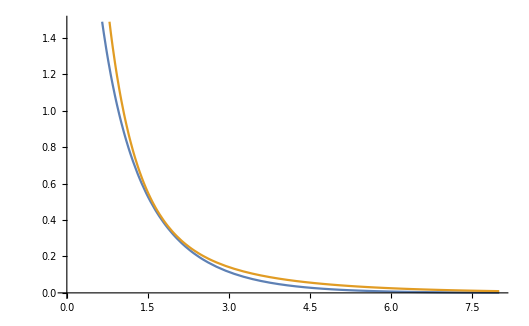

```mathematica
Plot[{(16/(3Pi))BesselK[0,0.8109599250271249 r],Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,0,8}]
```

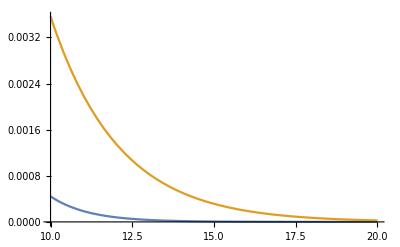

```mathematica
Plot[{(32/(3Pi))BesselK[0,0.8109599250271249 r],Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,10,20},PlotRange->All]
```

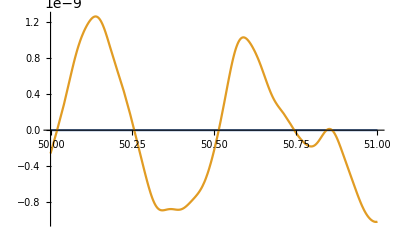

```mathematica
Plot[{(32/(3Pi))BesselK[0,0.8109599250271249 r],Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,50,51},PlotRange->All]
```

```mathematica
Plot[{(32/(3Pi))BesselK[0,0.8109599250271249 r]/Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]},{r,50,51},PlotRange->All]
```

```mathematica
BesselK[0,0.8109599250271249 r]/Log[E,1/r]
```

BesselK[0,0.81096 r]/Log[1/r]

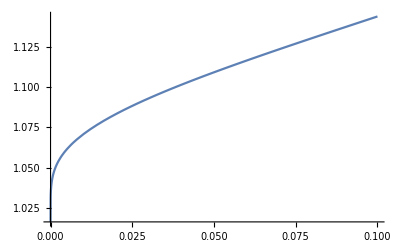

```mathematica
Plot[BesselK[0,0.8109599250271249 r]/Log[1/r],{r,0,0.1}]
```

```mathematica
D[g Hypergeometric0F1[3,-b^2(1-c t)/4],t]
```

1/12 b^2 c g Hypergeometric0F1[4,-1/4 b^2 (1-c t)]

```mathematica
Solve[1/12 b^2 c g==b^3/(8Gamma[4]),g]
```

{{g→b/(4 c)}}

```mathematica
Gamma[4]
```

6

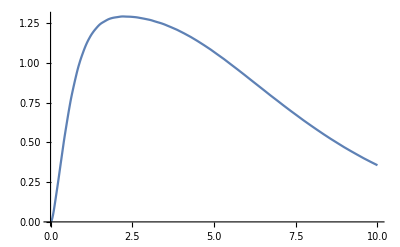

```mathematica
Plot[Sum[r/(2 π)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.164414,0.01}],{r,0,10},PlotRange->All]
```

```mathematica
Plot[(∫_({a,θ}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤2π,{a,θ}]) (BesselJ[2,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ]))))/(2 a π^2))/((2/Pi)Log[E,1/r]),{r,0,0.1}]
```

$Aborted

```mathematica
Limit[BesselK[0,Sqrt[0.164414]r]/Log[E,1/r],r->0]
```

```mathematica
∫_({a,θ}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤2π,{a,θ}]) (BesselJ[2,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ]))))/(2 a π^2)
```

∫_({a,θ}∈ImplicitRegion[147.973>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤2 π,{a,θ}]) (BesselJ[2,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ]))))/(2 a π^2)

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[147.97297337979867>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤2 π,{a,θ}]) (BesselJ[2,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ]))))/(2 a π^2)/((2/Pi)Log[E,1/r]),{r,0,0.01}]
```

```mathematica
Plot[{(32/(3Pi))BesselK[0,0.8109599250271249 r],Sum[1/(2 π r)(x (2/Max[x,0.000005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.00001),{x,0,2/0.164414,0.00001}]},{r,200,201},PlotRange->All]
```

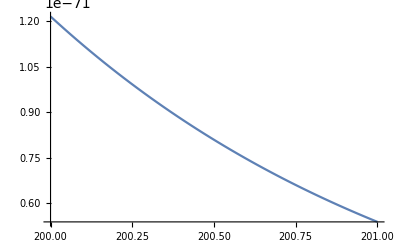

```mathematica
Plot[(32/(3Pi))BesselK[0,0.8109599250271249 r],{r,200,201},PlotRange->All]
```

```mathematica
Plot[{(32/(3Pi))BesselK[0,0.8109599250271249 r],Integrate[1/(2 π r)(x (2/x-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)]),{x,0,2/0.164414}]},{r,200,201},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.16792}. NIntegrate obtained -3.45116×10^-12 and 1.67279×10^-10 for the integral and error estimates.

$Aborted

```mathematica
Plot[∫_({a,θ}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2),{r,200,201}]
```

$Aborted

```mathematica
Subscript[J, 3][r_]=Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]
```

Power::infy: Infinite expression 1/0. encountered.

0.+(0.636515 (Hypergeometric0F1[3,-1999.84 1]-1))/r+(0.318205 1)/r+12159+2411/r+(7.07445×10^-13 (1-1))/r+(6.06861×10^-14 (Hypergeometric0F1[3,-5.59882×10^-6 (147.963-24.328 r+r^2)]-Hypergeometric0F1[3,-22 1]))/r
 |  |  |  |

```mathematica
Subscript[J, 4][r_]=Sum[1/(2 π r)(x (2/Max[x,0.00005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.0001),{x,0,2/0.164414,0.0001}]
```

Power::infy: Infinite expression 1/0. encountered.

0.+(0.636609 (Hypergeometric0F1[3,-19999.8 1]-1))/r+(0.318299 1)/r+121639+2311/r+(4.6144×10^-16 (1-1))/r+(7.1543×10^-18 (Hypergeometric0F1[3,-1.92233×10^-7 (147.973-24.3288 r+r^2)]-Hypergeometric0F1[3,1]))/r
 |  |  |  |

```mathematica
Subscript[J, 4][100]
```

2.67304×10^-12

```mathematica
Subscript[J, 5][r_]=Sum[1/(2 π r)(x (2/Max[x,0.000005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.00001),{x,0,2/0.164414,0.00001}]
```

$Aborted[]

```mathematica
Subscript[J, 6][r_]=Sum[1/(2 π r)(x (2/Max[x,0.0000005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.000001),{x,0,2/0.164414,0.000001}]
```

```mathematica
Subscript[n, 3(10)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

∫_({a,θ}∈ImplicitRegion[147.973>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)

```mathematica
Subscript[n, 3(10)][100]
```

-7.90288×10^-11-4.02366×10^-57 ⅈ

```mathematica
Subscript[n, 3(10)][200]
```

7.53723×10^-12

```mathematica
Subscript[n, 3(10)][1000]
```

-4.74493×10^-13-3.66631×10^-52 ⅈ

```mathematica
Subscript[S, 4][r_]=0.0001 r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.00005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]],{x,0,2/0.164414,0.0001}]
```

Power::infy: Infinite expression 1/0. encountered.

(0.0001 (0.+1.24716×10^-8 BesselJ[3,0.000876888 r]+121642+0.0282839 BesselJ[3,282.842 r]))/r^3
 |  |  |  |

```mathematica
Subscript[S, 5][r_]=0.00001 r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.000005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/Max[x,0.000005]]],{x,0,2/0.164414,0.00001}]
```

$Aborted

```mathematica
Subscript[S, 6][r_]=0.000001 r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.0000005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]],{x,0,2/0.164414,0.000001}]
```

```mathematica
x^2 Sqrt[-0.164414+2/Max[x,0.00005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]]
```

x^2 BesselJ[3,2 r √(-0.164414+2/x)] (-0.164414+2/Max[0.00005,x])^(3/2)

```mathematica
0.00001(100)^-3 Sum[(-0.164414x+2)^(3/2) x^(1/2)BesselJ[3,200 Sqrt[-0.164414+2/Max[x,0.000005]]],{x,0,12.16441422263311,0.00001}]
```

$Aborted

```mathematica
0.000001(100)^-3 Sum[(-0.164414x+2)^(3/2) x^(1/2)BesselJ[3,200Sqrt[-0.164414+2/x]],{x,0,12.16441422263311,0.000001}]
```

```mathematica
(-0.164414x+2)^(3/2) x^(1/2)
```

```mathematica
2/0.164414
```

12.1644

```mathematica
ScientificForm[12.16441422263311]
```

1.21644×10^1

```mathematica
NumberForm[12.16441422263311,8]
```

12.164414

```mathematica
NumberForm[12.16441422263311,16]
```

12.16441422263311

```mathematica
NumberForm[12.16441422263311,16]
```

12.16441422263311